# Lab 12: Momentum and Angular Momentum in Two Dimensions

In this lab you will film pucks on an air table and use the video to study the conservation of momentum and angular momentum in two dimensions.

### Theory

#### Basics

Earlier we studied one dimension collisions on an air track. Now, we want to study two dimensional collisions on an air table, which are much more complicated than one dimensional ones. To begin, with we will assume that our pucks are point particles. Of course, they are actually disks and in the next section we will take their shape and size into account. 

A general two body, two dimensional collision is shown in the figure below. We will choose our coordinates so that the mass m_2 is initially at rest and at the origin; we can do this without loss of generality since there is always a reference frame in which m_2 is at rest (this is true if m_2is not accelerating, which we will assume to be case). We will also point our axes so that the mass m_1has an initial velocity only in the x direction, again, without loss of generality.  

The parameter b in the diagram is called the “impact parameter”. The solid circles represent the particles before the collision, while the dashed circles represent the particles after the collision. The classical collision shown below is an example of a more general physical interaction called scattering.

#### Point Particles

In a scattering experiment you usually know the initial velocities of the particles and you want to calculate, or measure the final velocities of the particles. In a one dimensional collision we can calculate the final velocities of the particles if the collision is elastic. If the collision is inelastic we need to measure the final velocity of at least one of the particles, or we must know something about the dynamics of the collision. As we will see the two dimensional case is more complicated.
	What can we say about the collision from the kinematics alone? Well, it’s fair to say that we don't know anything about the forces acting on the particles during the collision.  In general, all we know is that momentum, angular momentum and the total energy of the system is conserved. Knowing that the total energy is conserved is not very useful since there is no guarantee that the mechanical energy is conserved. In fact mechanical energy will be conserved only in an elastic collision. 
	
From momentum conservation we know that 
	p_(1i x)=p_(1f) cos(ϕ) + p_(2f) cos(θ) and  0= p_(1f) sin(ϕ)+p_(2f) sin(θ)	 (1).
Translating this into Mathematica code gives:

```mathematica
pxEquation=m1 v1i==m2 v2f Cos[θ]+m1 v1f Cos[ϕ];
pyEquation=0==m2 v2f Sin[θ]+m1 v1f Sin[ϕ];
```

Notice that we have four unknowns (two angles and two speeds) and only two equations. Of course, we have not yet conserved angular momentum; maybe that will be useful.  Recall that for a point particle L=r ×p where r is the distance that the particle is from the origin. 

So (see the figure above), the initial angular momentum is L_i=-b m_1 v_(1i) ẑ. Since the velocities and motion of the particles are in the x-y plane their angular momentum is in the z direction. The final angular momentum of the first particle  is 
m_1 v_(1f)(r_1  sin(ϕ)- r_1 cos(ϕ)) ẑ and the final angular momentum of the second is m_2 v_(2f)(r_2  sin(θ)- r_2 cos(θ)) ẑ where r_1=√(x_1^2+y_1^2) and  r_2=√(x_2^2+y_2^2). Thus

 b m_1 v_(1i)= m_1 v_(1f)( r_1 cos(ϕ)-r_1  sin(ϕ)) +m_2 v_(2f)(r_2 cos(θ)-r_2  sin(θ) )  	(2).
  
This does not help us much, since in order to calculate the position of a particle we have to know how much time has elapsed since the collision.

Thus, in general we will have to measure two quantities in the final state of a two body collision. These can be any combination of angles and or velocities.

If the collision is elastic, and in general it is not, then kinetic energy is conserved:

1/2 m_1(v_(1i))^2=1/2 m_1(v_(1f))^2+1/2 m_2 (v_(2f))^2						(3)

This would give us a third equation to use, and we would only need to measure one final state quantity in order to determine all the rest.

```mathematica
KEEquation=m1 v1i^2==m1 v1f^2+m2 v2f^2;
```

```mathematica
angleEquation=Simplify[Eliminate[{pxEquation,pyEquation,KEEquation},{v1f,v2f}]]
```

m1 v1i Sin[ϕ] (m2 Sin[2 θ-ϕ]+m1 Sin[ϕ])==0

```mathematica
Solve[angleEquation,θ]
```

{{θ→ConditionalExpression[1/2 (ϕ-ArcSin[(m1 Sin[ϕ])/m2]+2 π C[1]),C[1]∈Integers]},{θ→ConditionalExpression[1/2 (π+ϕ+ArcSin[(m1 Sin[ϕ])/m2]+2 π C[1]),C[1]∈Integers]}}

In the above equation, we have eliminated v_(1f), v_(2f) and θ, and would only need to measure ϕ to completely determine the system.  (We could have chosen a different variable to measure if we wanted to.)

#### Disks

We now relax the assumption that our pucks are point particles and treat them as disks (which, of course, is what they are). This means that they can rotate, which affects both their angular momentum and their kinetic energy.  The linear momentum is unchanged. 

To start, we will assume that the stationary disk is not rotating. The initial kinetic energy of the of the system is now K_i = 1/2 m_1 (v_(1i))^2+1/2 I_1 (ω_(1i))^2 where I_1 is the  moment of inertia for the first puck and ω_(1i) is the initial angular velocity of the first puck. 

Note that in our case the linear speed and the angular speed are not related (v≠ ω r)! 

The final kinetic energy of the system is 
K_f=1/2 m_1 (v_(1f))^2+1/2 I_1 (ω_(1f))^2+1/2 m_2 (v_(2f))^2+1/2 I_2 (ω_(2f))^2  where the subscripts are self-explanatory. 
Thus, if the collision is elastic, we have (instead of Eqn. (3) )

1/2 m_1 (v_(1i))^2+1/2 I_1 (ω_(1i))^2=1/2 m_1 (v_(1f))^2+1/2 I_1 (ω_(1f))^2+1/2 m_2 (v_(2f))^2+1/2 I_2 (ω_(2f))^2	(4).

For disks we know that I=1/2 m R^2 where m is the mass of the disk and R is the radius of the disk. 

The angular momentum of the system now has contributions from two sources: 
· The r× p terms, which are akin to "orbital" angular momentum about the origin, and 
· The I ω terms, which come from the rotation of each puck about their own axis. 
It is the sum of these two contributions (orbital + rotational) that is conserved; they are not conserved individually!

The initial angular momentum of the system is 

L_i=b m_1 v_(1i)+I_1 ω_(1i)  
while the final angular momentum is 
L_f= m_1 v_(1f)( r_1 cos(θ)-r_1  sin(θ)) +m_2 v_(2f)(r_2 cos(ϕ)-r_2  sin(ϕ) ) +I_1 ω_(1f)+I_2 ω_2.
Thus, conservation of angular momentum gives

b m_1 v_(1i)+I_1 ω_(1i)=  m_1 v_(1f)( r_1 cos(θ)-r_1  sin(θ)) +m_2 v_(2f)(r_2 cos(ϕ)-r_2  sin(ϕ) ) +I_1 ω_(1f)+I_2 ω_2 (5)

The goal of this experiment is to verify Eqn. (1) and Eqn. (2) for the case in which the disks are not spinning and Eqn. (1) and Eqn. (5) if the disks are spinning. We also want to check to see if the collisions are elastic. We can do this by computing 
ϵ = -ΔK/K_i= -(K_f- K_i)/K_i . 

Note that if the collision is elastic ϵ=0 while if the collision is completely inelastic (the particles stick together) we have ϵ= m_2/(m_1+m_2).

### Taking Data

#### Experimental Setup

The set up will consist of an air table over which we will position a camera. You want to do three experiments, the first should be a collision between a stationary puck and a moving puck with neither puck spinning. You should then repeat the experiment but this time spin the puck you are going to slide into the stationary puck. For your last experiment use two pucks with velcro and spin the moving puck. To capture the video we will use a high speed digital camera and it's related software.  Once you have your video captured, copy the movie to a USB disc. Make sure that you give your file a unique name. You can now analyze your data from any computer (Mac or PC) in room 300.

Read This!

There are three critical points to remember when taking your data:
1) You will need to be able to convert from pixels to meters. To enable you to do this you should place a meter stick at the edge of the air table when filming. This will allow you to calculate a scale factor for converting distances in pixels to meters.

2) Make sure you capture you video at about 59.37 frames per second. This option is set via the camera's software interface. The choice of this frequency eliminates flicker from the lights and allows a sufficient number of frames to be analyzed before and after the collisions.

3) Make sure that you start filming before you launch the puck and keep filming until the pucks hit the edges of the air table. Since Mathematica allows you to select the start and end frames when analyzing your film you can afford to film a few extra seconds (not minutes) of video.

#### Obtaining the Data from the Video

To obtain the data from your video you  have to  extract the positions of the pucks (and their rotation rates) from the video.  Once the video is captured you will need to use either the software ImageJ or use Mathematica. There will be a demonstration using both of these applications at the beginning of the class. After the data has been collected we can import the data sets into Mathematica in the usual way.

This “Import” statement is not expected to work; it (and the statements below which depend on it) is (are) only included so that you see what the code looks like.  Your statements can be based on these, but will be changed somewhat.

```mathematica
SetDirectory["/home/patrick/Lab11"];
YellowPixels=Import["YellowPixelData.txt","Table"];
MagentaPixels=Import["YellowPixelData.txt","Table"];
GreenPixels=Import["YellowPixelData.txt","Table"];
CyanPixels=Import["YellowPixelData.txt","Table"];
```

We will also need the time information.  We capture our data at or near 59.37 fps. Your lab instructor will give you the framerate of the camera. You can use this framerate to generate a list of accurate time data.

```mathematica
framerate=59.37;
TimeData=Table[i,{i,0,Length[YellowPixels]/framerate-1/framerate,1/framerate}];
```

Now that we have the puck positions we can start reconstructing the collision. We need to scale may data which is currently in units of pixels. From looking at the meter stick that was placed on the air table you can make a measurement of the length in pixels of the meter stick. To do this you should use the “Get Coordinates” function in drawing tools of Mathematica (Right click on a frame from your movie and select “Get Coordinates”). Be sure to write down your estimation of the error involved in this measurement (please ask if you are unsure of what this ‘estimation’ is).

```mathematica
scale=749.0-176.0;
```

If you divide the puck positions by the scale factor you will get the positions in meters not pixels.

```mathematica
YellowData=YellowPixels/scale;
GreenData=GreenPixels/scale;
MagentaData=MagentaPixels/scale;
CyanData=CyanPixels/scale;
```

```mathematica
plot1=ListPlot[YellowData,PlotStyle->Yellow,AxesLabel->{"x","y"},PlotRange->All]
```

```mathematica
plot2=ListPlot[MagentaData,PlotStyle->Magenta,AxesLabel->{"x","y"},PlotRange->All]
```

The plot below should show the collision. The lines do not touch, since the positions are for the puck centers and the pucks have a finite size.

```mathematica
Show[plot1,plot2]
```

### Data Analysis

#### Plots

We can now check to see if linear momentum is conserved. To do this we need to look at the motion in the x and y directions as a function of time. The plot above shows y(x), we want y(t) and x(t). We can extract the x and y positions using replacement rules. We can then combine the x (and y) data with the our time data.

```mathematica
xYellowPosition=Transpose[{TimeData,YellowData/.{x_,y_}->x}];
yYellowPosition=Transpose[{TimeData,YellowData/.{x_,y_}->y}];
xMagentaPosition=Transpose[{TimeData,MagentaData/.{x_,y_}->x}];
yMagentaPosition=Transpose[{TimeData,MagentaData/.{x_,y_}->y}];
```

We should plot the data to make sure that it makes sense.

```mathematica
ListPlot[xYellowPosition,PlotLabel->"Yellow Puck",AxesLabel->{"t","x"}]
ListPlot[yYellowPosition,PlotLabel->"Yellow Puck",AxesLabel->{"t","y"}]
ListPlot[xMagentaPosition,PlotLabel->"Magenta Puck",AxesLabel->{"t","x"}]
ListPlot[yMagentaPosition,PlotLabel->"Magenta Puck",AxesLabel->{"t","y"}]
```

The pucks move in a straight line except at the instant of the collision. Thus, except at the instant of the collision each puck's position is given by x(t) = x_0+v_(0x)t , y(t)=y_0+v_oy t. We can describe the motion of the puck  over the entire collision by x(t) = x_(0i)+ v_(0xi)t  if t< t_collision and  x(t) = x_(0f)+ v_(0xf)t  if t>t_collision.With a similar expression for y(t). We can use NonlinearModelFit to find all these parameters including t_collision.
The model that we will use is just the one given above with x_(0f)(and y_(0f)) chosen so that the puck's path is continuous although not smooth.

```mathematica
model:=If[t≤tCollision,v0i t+ x0i,v0f t+x0i+tCollision(v0i-v0f)]

xYellowFit=NonlinearModelFit[xYellowPosition,model,{v0i,x0i,v0f,tCollision},t]
```

We can extract the actual function and the parameters with

```mathematica
xYellowFit[t]
xYellowFit["ParameterTable"]
```

This tells us that the collision occurred at 
t=0.374 seconds, v_(0xi)=-0.111m/s and v_(0xf)=-0.286m/s.
Checking the fit show that it is very good,

```mathematica
plota=Plot[xYellowFit[t],{t,0,1.4}];
plotb=ListPlot[xYellowPosition,PlotStyle->Red];
Show[plota,plotb]
```

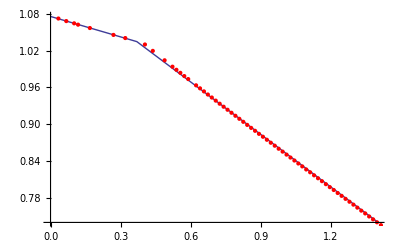

We can now do the same thing for the y position and for the yellow puck.

```mathematica
yYellowFit=NonlinearModelFit[yYellowPosition,model,{v0i,x0i,v0f,tCollision},t]
```

```mathematica
plotc=Plot[yYellowFit[t],{t,0,1.4}];
plotd=ListPlot[yYellowPosition,PlotStyle->Red];
Show[plotc,plotd]
```

Now we should do the same analysis for the magenta puck

```mathematica
xMagentaFit=NonlinearModelFit[xMagentaPosition,model,{v0i,x0i,v0f,tCollision},t]
```

```mathematica
plote=Plot[xMagentaFit[t],{t,0,1.4}];
plotf=ListPlot[xMagentaPosition,PlotStyle->Red];
Show[plote,plotf]
```

Now for the magenta pucks y data:

```mathematica
yMagentaFit=NonlinearModelFit[yMagentaPosition,model,{v0i,x0i,v0f,tCollision},t]
```

Which gives an initial velocity of zero and v_(0fyLarge)=-0.41 m/s. The fit is good as well.

```mathematica
plotg=Plot[yMagentaFit[t],{t,0,1.4}];
ploth=ListPlot[yMagentaPosition,PlotStyle->Red];
Show[plotg,ploth]
```

Finally, to summarize we have :

```mathematica
Print["Yellow disk x fit"]
xYellowFit["ParameterTable"]
Print["Yellow disk y fit"]
yYellowFit["ParameterTable"]
Print["Magenta disk x fit"]
xMagentaFit["ParameterTable"]
Print["Magenta disk y fit"]
yMagentaFit["ParameterTable"]
```

#### Linear Momentum

When I weighed the pucks (your pucks may be different; make sure you weigh them!) I found that the yellow puck weighed 0.0475 Kg and the magenta puck 0.0460 Kg. Labeling the yellow puck 1 and the magenta puck 2 we have:

```mathematica
m1=0.0475;
v1ix=-0.111;
v1fx=-0.285;
v1iy=-0.412;
v1fy=-0.275;

m2=0.0460;
v2ix=-0.296;
v2fx=-0.0397;
v2iy=-0.187;
v2fy=-0.363;
```

We can now check momentum conservation (remember that we must conserve in the x and y directions separately). The units are the standard SI units of  Kg m/s.

```mathematica
pix= m1 v1ix+m2 v2ix
```

```mathematica
pfx=m1 v1fx+m2 v2fx
```

```mathematica
piy= m1 v1iy+m2 v2iy
```

```mathematica
pfy=m1 v1fy+m2 v2fy
```

To check to see how close the initial and final momentum are we compute |(p_ix-p_fx)/p_ix|and |(p_iy-p_fy)/p_iy|. This shows that we conserve momentum only at the 18% level in the x direction but that we conserve momentum at the 5% level in the y direction. The reason we do so badly in the x direction is that fit for the magenta disk in the x direction is not very good.

```mathematica
Abs[(pix-pfx)/pix]
```

```mathematica
Abs[(piy-pfy)/piy]
```

Another way of expressing the result would be to look at (p_i ·p_i-p_f·p_f)/p_i ·p_iwhere we consider p_i and  p_fas vectors.

```mathematica
pi={pix,piy};
pf={pfx,pfy};
```

The method weights the small components less and show that we conserve momentum to better than 2.5%.

```mathematica
Abs[(pi.pi-pf.pf)/(pi.pi)]
```

#### Angular Momentum

We now turn to the rotational motion of the system. We have already extracted the position of the dots above.

```mathematica
ListPlot[GreenData,PlotStyle->Green,PlotRange->All]
ListPlot[CyanData,PlotStyle->Cyan]
```

To recover the rotation rate we need to subtract off the pucks center of mass position so the we get the motion relative to the pucks center of mass.

```mathematica
YellowRotation=GreenData-YellowData;
ListLinePlot[YellowRotation,PlotStyle->Green]

MagentaRotation=CyanData-MagentaData;
ListLinePlot[MagentaRotation,PlotStyle->Cyan]
```

The next step is to convert to polar coordinates so that we can plot cos(θ) as a function of t where θ is the angle through which the puck has rotated. Recall that x=r cos(θ) so that  cos(θ)=x/r =x/√(x^2+y^2).

```mathematica
MagentaRotationPolar=MagentaRotation/.{x_,y_}->x/√(x^2+y^2);
MagentaPuckRotationData=Transpose[{TimeData,MagentaRotationPolar}];
```

Plotting this shows how the rotation of the Magenta puck changes as a result of the collision.

```mathematica
plotR1=ListPlot[MagentaPuckRotationData,Joined->True]
```

It is easier to see what is going on if we mark the point at which the collision occurred.

```mathematica
CollisionPoint=Graphics[{PointSize[0.03],RGBColor[1,0,0],Point[{0.33,0}]}];

Show[plotR1,CollisionPoint]
```

The easiest way to obtain the angular frequency before and after the collision is to read them off from the graph. The time difference between the peak to peak height is the period T=(2π)/ω. The peaks I used to find ω_i (before the collision) and ω_f (after the collision) are marked with blue and green dots respectively.

```mathematica
markerPoints=Graphics[{{PointSize[0.025],RGBColor[0,1,0],Point[{0.038,1.01}],Point[{0.284,0.942}]},{PointSize[0.025],RGBColor[0,0,1],Point[{0.652,0.996}],Point[{1.01,1.01}]}}];

Show[plotR1,CollisionPoint,markerPoints]
```

Using these points gives T_1=0.25 sec and T_2= 0.36 sec, where T_1 is the period before the collision and T_2 is the period after the collision.

```mathematica
T1=0.25;
T2=0.36;
ω1=2π/T1
ω2=2π/T2
```

Next, we turn our attention to the Yellow puck.

```mathematica
YellowRotationPolar=YellowRotation/.{x_,y_}->x/√(x^2+y^2);

ListPlot[Transpose[{TimeData,YellowRotationPolar}],Joined->True,PlotLabel->"Yellow Puck Rotation"]
```

The initial rotation rate of the Yellow puck is zero.  It's hard to know for sure from my data but looks like my puck goes through half a period in 0.78 second so T_Yellow= 1.6 sec.

```mathematica
TYellow=1.6;
ωYellow=2π/TYellow
```

We will also need the moments of inertia for the pucks. The pucks are disks so their moment of inertia is I= 1/2 m r^2. The radius of the Magenta puck is r_Magenta= 0.0345 meters. The radius of the Yellow puck is r_Yellow=0.044 meters. Thus

```mathematica
rYellow= 0.044;
rMagenta=0.0345;
IYellow=1/2 m1 rYellow^2
IMagenta=1/2 m2 rMagenta^2
```

Remember that the units for I are kg m^2. We can now calculate the rotation kinetic energies of the pucks.

```mathematica
KMagentaInitial=1/2 IMagenta ω1^2
```

```mathematica
KMagentaFinial=1/2 IMagenta ω2^2
```

```mathematica
KYellowFinal=1/2 IYellow ωYellow^2
```

The position of the Magenta puck relative to the origin is given by PhysicalMagentaPuckCMPosition. Recall that L=r×p +I_Magenta ω_Magenta ẑ. Since the displacement  r and the momentum p are in the same  direction we expect that the r×p term will be zero to within  experimental error.  In order to compute the angular momentum we must do two things. We need to make both the momentum vector and the position vector three vectors. That is vector in {x,y,z}. The reason for this is that the momentum and position have components only in the x-y plane and thus the angular momentum will point in the z  direction. In order to get Mathematica to properly take the cross product we must and a zero component in the z direction to both p and r.

```mathematica
p=m2 {v2ix,v2iy,0}
```

```mathematica
RMagenta=MagentaData/.{x_,y_}->{x,y,0};
```

The other thing that we need to do is to shift the origin of r so that the pucks position starts at {0,0}. We need both p and r to be measured from the same origin. Since the origin of p is {0,0} we will shift r so that it's origin is also at {0,0}. We can do this simply be subtracting the first element of r from each element of the list.

```mathematica
r=RMagenta/.{x_,y_,z_}->{x,y,z}-First[RMagenta]
```

The next step is to compute the cross product. We have two lists (r and p). The elements of r are themselves three element lists representing a three vector. We want to take the cross product of each element of r with  p. To take the cross product of two vectors in ℝ^3we can use Cross. For example:

```mathematica
Cross[{x1,y1,z1},{x2,y2,z2}]
```

#### A digression for Mathematica Geeks, others may skip down

However, what we have are a list of vectors and a vector. We can not apply Cross directly to our list because we want the first argument to Cross to be a vector from the list of vectors in r and the second argument to be the vector  p . We can do this using Map.  The function Map maps functions across lists. For example:

```mathematica
Map[f,{a,b,c}]
```

maps the function f across the list.

Now consider two symbolic lists. The first list "list1" has the same structure as r. It is a list of three element list. The second list "vector" is just a three element list.

```mathematica
list1={{a1,b1,c1},{a2,b2,c2}}
```

```mathematica
vector={x1,y1,z1}
```

We can not just use Map since Cross takes two arguments, one of which we want to be constant. The code below will do what we want.

```mathematica
Map[Cross[#,vector]&,list1]
```

You will notice two odd things about this code. The # sign and the &. The # represents an argument to a pure Function and the & tags the function as a pure function. An example or two will make things much clearer. Suppose I want to write a function that squares its arguments. One way to do this is

```mathematica
h[x_]:=x^2
```

```mathematica
h[12]
```

```mathematica
h[1+y]
```

This is a named function. I called it h. A pure function has no name. To do the same thing using a pure function we write

```mathematica
#^2&[x]
```

The syntax tells the kernel to take whatever is in the square brackets and square it.The & tells the kernel that we have a pure function. If we leave it out we get

```mathematica
(#^2)[x]
```

Here is a slightly more complicated example:

```mathematica
(#^3+#)&[1+z]
```

Why, you ask would we ever want to do this? Pure functions are not very useful by themselves but are very powerful when combined with Map. Let us go back to our to lists; "list1" and "vector".

```mathematica
Map[f[#,vector]&,list1]
```

Notice that if the function f was the cross product we would get exactly what we want,

```mathematica
Map[Cross[#,vector]&,list1]
```

that is we have taken the cross product of each vector in the list "list1" with the vector "vector".

#### Back to the angular momentum

The same method will allows use to compute the angular momentum. We are interested in only the first 11 elements of r since they are the elements that refer to the position before the collision.

```mathematica
LMagenta=Map[Cross[#,p]&,Take[r,{1,11}]]
```

Notice that as expected the angular momentum from the term r×p is essentially zero. The largest values are an order of magnitude smaller than the contribution from the I ω term. The contribution from the I ω term is:

```mathematica
IMagenta ω1
```

and this is the only term that contributes to the initial angular momentum.  Thus we have

```mathematica
Li=IMagenta ω1
```

After the collision we have four terms. L_total= I_Magentaf ω_Magentaf ẑ+I_Yellowf ω_Yellowf ẑ+r_Yellowf×p_Yellowf+r_Yellowf×p_Yellowf, where the f refers to the final state (i.e. after the collision). The rotational (I ω) terms give

```mathematica
IMagenta ω2
```

```mathematica
IYellow ωYellow
```

In order to decide of these terms point in the positive or negative z-direction you will have to look at the video and see if they are rotating in the clockwise (negative z axis) or counter-clockwise (positive z-axis) direction. In my case they are both clockwise.

```mathematica
Lrot=IMagenta ω2+IYellow ωYellow
```

Notice that the rotational angular momentum is conserved to with in about 4%. 

However, there is no requirement that the Iω pieces and the r×p terms be separately conserved. Only the total angular momentum need be conserved.

```mathematica
100 Abs[Li-Lrot]/Li
```

In order to check the  r×p terms we must shift the origin of the Yellow puck position so that we are measuring the positions of the Yellow puck from the same origin as the Magenta puck. This is done in the code below.

```mathematica
RYellow=YellowData/.{x_,y_}->{x,y,0};

RYellowShifted=RYellow/.{x_,y_,z_}->({x,y,z}-First[RMagenta])
```

We will also need the final momentums of the Yellow and Magenta pucks.

```mathematica
pMagentaf=m2{v2fx,v2fy,0}

pYellowf=m1{v1fx,v1fy,0}
```

We can now compute the r×p terms for both pucks. We expect them to be constant but not zero.

```mathematica
LMagentaf=Map[Cross[#,pMagentaf]&,Take[r,{12,44}]]

LYellowf=Map[Cross[#,pYellowf]&,Take[RYellowShifted,{12,44}]]
```

The plot below is deceiving. The points look scattered but look at the scale.

```mathematica
plotL1=ListPlot[LYellowf/.{x_,y_,z_}->z,AxesLabel->{"Frame #","L"}];
plotL2=ListPlot[LMagentaf/.{x_,y_,z_}->z,AxesLabel->{"Frame #","L"},PlotStyle->RGBColor[1,0,0]];

Show[plotL1,plotL2]
```

Shown on the same plot, we see that the r×p terms are constant after the collision as they must be since after the collision there are no external torques.

Since the total angular momentum must be conserved and the I ω pieces were conserved separately we expect LYellowf and LMagentaf to cancel. We can see from the graph that they have opposite signs. Adding them gives

```mathematica
LA=(LYellowf+LMagentaf)/.{x_,y_,z_}->z
```

This looks small but small compared to what? Whenever we say something is small we need to compare it with something, and we would like the comparison to be dimensionless (otherwise we could make it large or small just by changing from meters to millimeters, for example). 

The relevant quantity to compare to is the norm of LYellowf (or LMagentaf). Remember the norm of a vector v is √(v.v) and tells us the vector length or magnitude.

```mathematica
norm=√((LYellowf/.{x_,y_,z_}->z).(LYellowf/.{x_,y_,z_}->z))
```

La/norm is a dimensionless quantity that we can compare to 1 since in the absence of any conservation we would expect it to be of order 1. Doing the comparison shows that it is indeed small and the r×p terms are separately conserved. Remember that this separate conservation  may not be true for your data.

```mathematica
LA/norm
```

## Upshot

This is a rough outline of the experiment.  This is not necessarily a complete list of what needs to be done.

1) There are a lot of steps!

2)

3)

4)

## Assignment

The assignment for Week 12 is a full Lab Report which addresses all relevant questions and results from this writeup, and reflects on each.  This report should be written in accordance with the general rules and guidelines of the Syllabus for this course; please ask if there are any questions about what specifically is required.